```mathematica
Nt = 100;
ti = 0; tf = 10; 
deltat = (tf - ti) /Nt ;
Nx = 100; 
xi = -2; xf = 8; 
deltax = (xf - xi) / Nx; 
c =  1;
r = c * (deltat / deltax)
method = "CN";
```

1

```mathematica
T = Table[tn = ti + n *deltat, {n, 0, Nt  }];
a = -2;
b = 8;

(*For Everything Else*)
X2=Table[(a+b)/2+(a-b)/2 Cos[i π/Nx],{i,0,Nx }]//N;
X = X2;

(*For Perodic Interpolation*) 
(*X = Table[xm = xi + m *deltax, {m, 0, Nx + 1}]//N;
(*For Everything Else*)
X2 =  Table[xm = xi + m *deltax, {m, 0, Nx }]//N;*)
```

```mathematica
L = (NDSolve`FiniteDifferenceDerivative[Derivative[1],X, "DifferenceOrder"->2 , PeriodicInterpolation -> True ]@"DifferentiationMatrix"//Normal);
L = -1 * c * L ;
L//MatrixForm;

I1 = IdentityMatrix[Length[L]];
```

```mathematica
U = Table[0, {n, 0, Nt}, {m, 0, Nx}];
```

```mathematica
f[x_] = Exp[-16* x^2];
U[[1,All]] = f[X2]//N;
```

```mathematica
U = Chop[N[U], 10^(-307)];
U = N[U];
U = Developer`ToPackedArray[U, Real]; 
Developer`PackedArrayQ[U]
```

True

```mathematica
(* Trapezoidal *)
Ut = Table[0, {n, 0, Nt}, {m, 0, Nx}];
Ut[[1,All]] = f[X2]//N;
Ut = Chop[N[Ut], 10^(-307)];
Ut = N[Ut];
Ut = Developer`ToPackedArray[Ut, Real]; 
Developer`PackedArrayQ[Ut]
```

True

```mathematica
A = I1 - ((deltat / 2) * L);
B = I1 + ((deltat / 2) * L);
M = Inverse[A].B;
Do[Ut[[n+1,All]] = M.Ut[[n,All]], {n,1,Nt}];

(* Euler *)
Ue = Table[0, {n, 0, Nt}, {m, 0, Nx }];
Ue[[1,All]] = f[X2]//N;
Ue = Chop[N[Ue], 10^(-307)];
Ue = N[Ue];
Ue = Developer`ToPackedArray[Ue, Real]; 
Developer`PackedArrayQ[Ue] 

Leuler = (NDSolve`FiniteDifferenceDerivative[Derivative[1],X, "DifferenceOrder"->1, PeriodicInterpolation -> True]@"DifferentiationMatrix"//Normal);
Leuler = -1 * c * Leuler ;
Leuler//MatrixForm;

Ieuler = IdentityMatrix[Length[Leuler]];

euler = Ieuler + deltat*Leuler;
Do[Ue[[n+1,All]] = euler.Ue[[n,All]], {n,1,Nt}];
```

True

```mathematica
(*TVD RK2*)
Urk = Table[0, {n, 0, Nt}, {m, 0, Nx }];
Urk[[1,All]] = f[X2]//N;
Urk = Chop[N[Urk], 10^(-307)];
Urk = N[Urk];
Urk = Developer`ToPackedArray[Urk, Real]; 
Developer`PackedArrayQ[Urk]

LRK2 = (NDSolve`FiniteDifferenceDerivative[Derivative[1],X, "DifferenceOrder"->2, PeriodicInterpolation -> True ]@"DifferentiationMatrix"//Normal);
LRK2 = -1 * c * LRK2 ;
LRK2//MatrixForm;

LRK22 = (NDSolve`FiniteDifferenceDerivative[Derivative[2],X, "DifferenceOrder"->2, PeriodicInterpolation -> True ]@"DifferentiationMatrix"//Normal);
LRK22//MatrixForm;

IRK2 = IdentityMatrix[Length[LRK2]];

Mrk = (IRK2 + (deltat * LRK2) + ((1/2)* (deltat^2) * (-c)^2 * LRK22));

Do[Urk[[n+1,All]] = Mrk.Urk[[n,All]], {n,1,Nt}];
```

True

```mathematica
(*RK4*)
Urk4 = Table[0, {n, 0, Nt}, {m, 0, Nx }];
Urk4[[1,All]] = f[X2]//N;
Urk4 = Chop[N[Urk4], 10^(-307)];
Urk4 = N[Urk4];
Urk4 = Developer`ToPackedArray[Urk4, Real]; 
Developer`PackedArrayQ[Urk4]

LRK41 = (NDSolve`FiniteDifferenceDerivative[Derivative[1],X, "DifferenceOrder"->4, PeriodicInterpolation -> True ]@"DifferentiationMatrix"//Normal);
LRK41//MatrixForm;

LRK42 = (NDSolve`FiniteDifferenceDerivative[Derivative[2],X, "DifferenceOrder"->4, PeriodicInterpolation -> True ]@"DifferentiationMatrix"//Normal);
LRK42//MatrixForm;

LRK43 = (NDSolve`FiniteDifferenceDerivative[Derivative[3],X, "DifferenceOrder"->4, PeriodicInterpolation -> True ]@"DifferentiationMatrix"//Normal);
LRK43//MatrixForm;

LRK44 = (NDSolve`FiniteDifferenceDerivative[Derivative[4],X, "DifferenceOrder"->4, PeriodicInterpolation -> True ]@"DifferentiationMatrix"//Normal);
LRK44//MatrixForm;

IRK4 = IdentityMatrix[Length[LRK41]];

Series[Exp[x],{x,0,4}]

RK4X = Table[c*deltat*ToExpression["LRK4"<>ToString[i]],{i,1,4}];

MRK4 = IRK4 + RK4X[[1]] + ((1/2) * (RK4X[[2]])) + ((1/6) * (RK4X[[3]])) + ((1/24) * (RK4X[[4]]));

Do[Urk4[[n+1,All]] = MRK4.Urk4[[n,All]], {n,1,Nt}];
```

True

1+x+x^2/2+x^3/6+x^4/24+O[x]^5

```mathematica
(*New Method*)
UN = Table[0, {n, 0, Nt}, {m, 0, Nx }];
UN[[1,All]] = f[X2]//N;
UN = Chop[N[UN], 10^(-307)];
UN = N[UN];
UN = Developer`ToPackedArray[UN, Real]; 
Developer`PackedArrayQ[UN]

LN1 = (NDSolve`FiniteDifferenceDerivative[Derivative[1],X, "DifferenceOrder"->4, PeriodicInterpolation -> True ]@"DifferentiationMatrix"//Normal);
LN1//MatrixForm;

LN2 = (NDSolve`FiniteDifferenceDerivative[Derivative[2],X, "DifferenceOrder"->4, PeriodicInterpolation -> True ]@"DifferentiationMatrix"//Normal);
LN2//MatrixForm;

IN = IdentityMatrix[Length[LN1]];

PadeApproximant[Exp[x],{x,0,{2,2}}]

XforNM = Table[c*deltat*ToExpression["LN"<>ToString[i]],{i,1,2}];

AN = IN - ((deltat / 2) * LN1) + ((1/12) * LN2);
BN = IN + ((deltat / 2) * LN1) + ((1/12) * LN2);
MN = Inverse[AN].BN;
Do[UN[[n+1,All]] = MN.UN[[n,All]], {n,1,Nt}];
```

True

(1+x/2+x^2/12)/(1-x/2+x^2/12)

Inverse::luc: Result for Inverse of badly conditioned matrix {{14577.,-21209.2,7929.66,-1475.61,191.6,-12.5031,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«51»},{9325.13,-12953.8,3998.91,-410.297,43.6843,-2.60473,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,«51»},«48»,«51»} may contain significant numerical errors.

```mathematica
(************************************************************************************************************************)

(* Eigenvalues*)
```

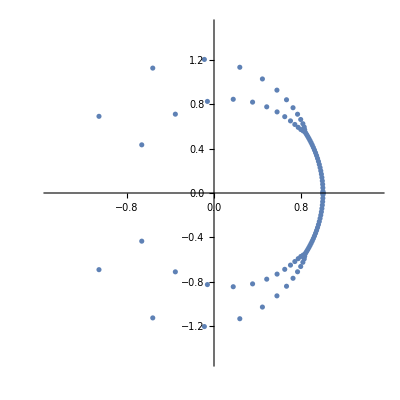

```mathematica
(*Trapezoidal*)
evals = Eigenvalues[N[M]];
realEvals = Re[evals];
imagEvals = Im[evals];
(*combinedEvals = Transpose[{realEvals,imagEvals}];*)
ListPlot[Transpose[{realEvals,imagEvals}],PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]
```

{39.5318,12.515,12.515,7.11437,7.11437,4.8017,4.8017,3.51838,3.51838,2.70296,2.70296,2.13948,2.13948,1.72717,1.72717,1.4127,1.4127,1.16517,1.16517,1.,1.,0.965458,0.965458,0.801107,0.801107,0.663636,0.663636,0.547081,0.547081,0.447123,0.447123,0.363275,0.363275,0.362647,0.362647,0.361385,0.361385,0.360559,0.360559,0.359486,0.359486,0.356939,0.356939,0.353731,0.353731,0.349846,0.349846,0.345264,0.345264,0.339961,0.339961,0.333908,0.333908,0.327073,0.327073,0.319418,0.319418,0.310899,0.310899,0.301466,0.301466,0.291062,0.291062,0.284963,0.284963,0.279621,0.279621,0.26707,0.26707,0.253324,0.253324,0.238286,0.238286,0.221847,0.221847,0.218465,0.218465,0.203879,0.203879,0.184237,0.184237,0.162755,0.162755,0.159598,0.159598,0.139239,0.139239,0.113462,0.113462,0.1072,0.1072,0.0851642,0.0851642,0.060334,0.060334,0.0540355,0.0540355,0.0197123,0.0197123,0.0182382,0.0182382}

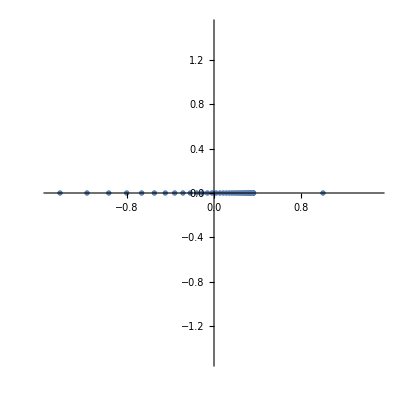

```mathematica
(*Euler*)
evalsEuler = Eigenvalues[N[euler]];
realEvalsEuler = Re[evalsEuler];
imagEvalsEuler = Im[evalsEuler];
Abs[evalsEuler]
ListPlot[{Transpose[{realEvalsEuler,imagEvalsEuler}]},PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]
```

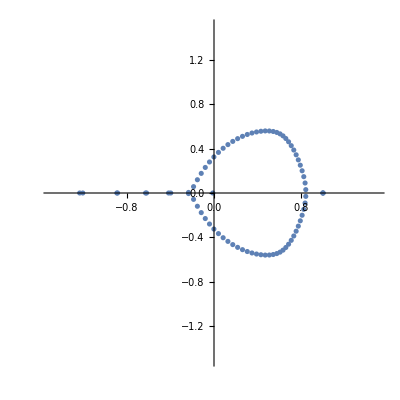

```mathematica
(*RK2*)
evalsRK2 = Eigenvalues[N[Mrk]];
realEvalsRK2 = Re[evalsRK2];
imagEvalsRK2 = Im[evalsRK2];
Abs[evalsRK2];
ListPlot[Transpose[{realEvalsRK2,imagEvalsRK2}],PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]
```

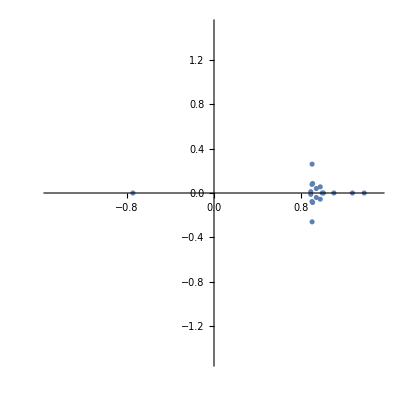

```mathematica
(*RK4*)
evalsRK4 = Eigenvalues[N[MRK4]];
realEvalsRK4 = Re[evalsRK4];
imagEvalsRK4 = Im[evalsRK4];
Abs[evalsRK4];
ListPlot[Transpose[{realEvalsRK4,imagEvalsRK4}],PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]
```

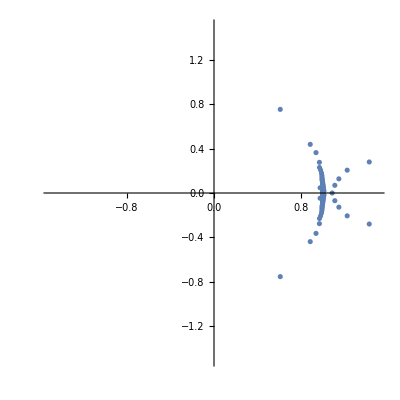

```mathematica
(*New Method*)
evalsN = Eigenvalues[N[MN]];
realEvalsN = Re[evalsN];
imagEvalsN = Im[evalsN];
Abs[evalsN];
ListPlot[Transpose[{realEvalsN,imagEvalsN}],PlotRange->{{-1.5,1.5},{-1.5,1.5}}, AspectRatio->1]
```

```mathematica
(************************************************************************************************************************)
(*Energy*)
```

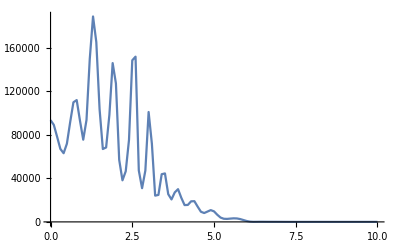

```mathematica
(*CN*)
weightsCN=π/(Nx+1)√((b-X2)(X2-a))//Simplify;
derivCN = (L.Ut)^2;
ECN = weightsCN.derivCN//N;
ListPlot[Transpose[{T,ECN}],PlotRange->All, Joined->True]
```

```mathematica
(*Euler*)
weightsEuler=π/(Nx+1)√((b-X2)(X2-a))//Simplify;
derivEuler = (Leuler.Ue)^2;
EEuler = weightsEuler.derivEuler//N;
ListPlot[Transpose[{T,EEuler}],PlotRange->All, Joined->True]
```

-Graphics-

```mathematica
(*RK2*)
weightsRK2=π/(Nx+1)√((b-X2)(X2-a))//Simplify;
derivRK2 = (LRK2.Urk)^2;
ERK2 = weightsRK2.derivRK2//N;
ListPlot[Transpose[{T,ERK2}],PlotRange->All, Joined->True]
```

ListPlot::prng: Value of option PlotRange -> {{0,10.},{0,5.39297338768275×10^341}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

-Graphics-

```mathematica
(*RK4*)
(*weightsRK4=π/(Nx+1)√((b-X2)(X2-a))//Simplify;
derivRK4 = (LRK41.Urk4)^2;
ERK4 = weightsRK4.derivRK4//N;
ListPlot[Transpose[{T,ERK4}],PlotRange->All, Joined->True]*)
```

```mathematica
(************************************************************************************************************************)
(*Export*)
(*exportData=Flatten/@Transpose[{realEvals,imagEvals}];
Export["C:\\Users\\eagle\\Desktop\\Research\\FD_Paper\\Data\\evals_"<>method<>"_"<>ToString[r]<>".dat",exportData,"Table"];*)
```

```mathematica
Animate[ListPlot[Table[Ut[[n+1, m+1]], {m,0,Nx}], PlotRange->{All,{0,2}}], {n,0,Nt,1}]
Animate[ListPlot[Table[Urk[[n+1, m+1]], {m,0,Nx}], PlotRange->{All,{0,2}}], {n,0,Nt,1}]
```

```mathematica
(************************************************************************************************************************)
```

```mathematica
PadeApproximant[Exp[x],{x,0,{1,1}}]
```

(1+x/2)/(1-x/2)

```mathematica
PadeApproximant[Exp[x],{x,0,{2,2}}]
```

(1+x/2+x^2/12)/(1-x/2+x^2/12)

```mathematica
PadeApproximant[Exp[x],{x,0,{3,3}}]
```

(1+x/2+x^2/10+x^3/120)/(1-x/2+x^2/10-x^3/120)

```mathematica
Series[Exp[x],{x,0,4}]
```

1+x+x^2/2+x^3/6+x^4/24+O[x]^5

```mathematica
Series[Exp[x],{x,0,2}]
```

1+x+x^2/2+O[x]^3